```mathematica
SetDirectory["C:\\Users\\benja\\OneDrive\\Documents\\GitHub\\KhovanovLaplacian\\basic_khovanov_testing"]
<< KnotTheory`
<< KhovanovLaplacian`
```

C:\Users\benja\OneDrive\Documents\GitHub\KhovanovLaplacian\basic_khovanov_testing

Get::path: ParentDirectory[File] in $Path is not a string.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[ParentDirectory[File],KnotTheory].

FileInformation::badfile: The specified argument, ToFileName[ParentDirectory[File],KnotTheory], should be a valid string or File.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[ToFileName[{File,WikiLink,mathematica}],KnotTheory].

FileInformation::badfile: The specified argument, ToFileName[ToFileName[{File,WikiLink,mathematica}],KnotTheory], should be a valid string or File.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[ToFileName[{File,QuantumGroups}],KnotTheory].

General::stop: Further output of ToFileName::strse will be suppressed during this calculation.

FileInformation::badfile: The specified argument, ToFileName[ToFileName[{File,QuantumGroups}],KnotTheory], should be a valid string or File.

General::stop: Further output of FileInformation::badfile will be suppressed during this calculation.

ReplaceAll::reps: {AbsoluteFileName→C:\Users\benja\OneDrive\Documents\GitHub\KhovanovLaplacian\basic_khovanov_testing\KnotTheory,AbsoluteShortFileName→C:\Users\benja\OneDrive\DOCUME~1\GitHub\KHOVAN~1\BASIC_~1\KNOTTH~1,Archive→True,BlockCount→Missing[NotAvailable],BlockSize→Missing[NotAvailable],ByteCount→12288,Compressed→Missing[NotAvailable],CreationDate→DateObject[{2024,3,13,16,49,29.},Instant,Gregorian,-4.],DirectoryName→C:\Users\benja\OneDrive\Documents\GitHub\KhovanovLaplacian\basic_khovanov_testing,Encrypted→Missing[NotAvailable],«23»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ParentDirectory::nums: Argument File/.{AbsoluteFileName→C:\Users\benja\OneDrive\Documents\GitHub\KhovanovLaplacian\basic_khovanov_testing\KnotTheory,AbsoluteShortFileName→C:\Users\benja\OneDrive\DOCUME~1\GitHub\KHOVAN~1\BASIC_~1\KNOTTH~1,Archive→True,BlockCount→Missing[NotAvailable],BlockSize→Missing[NotAvailable],ByteCount→12288,Compressed→Missing[NotAvailable],CreationDate→DateObject[{2024,3,13,16,49,29.},Instant,Gregorian,-4.],DirectoryName→C:\Users\benja\OneDrive\Documents\GitHub\KhovanovLaplacian\basic_khovanov_testing,Encrypted→Missing[NotAvailable],«23»} should be a positive machine-size integer, a nonempty string, or a File specification.

Loading KnotTheory` version of September 6, 2014, 13:37:37.2841.
Read more at http://katlas.org/wiki/KnotTheory.

Get::path: ParentDirectory[File] in $Path is not a string.

General::stop: Further output of Get::path will be suppressed during this calculation.

Get::noopen: Cannot open WikiLink`.

Needs::nocont: Context WikiLink` was not created when Needs was evaluated.

DeclarePackage::aldec: Symbol CreateWikiConnection in DeclarePackage[WikiLink`,{CreateWikiConnection,WikiGetPageText,WikiGetPageTexts,WikiSetPageText,WikiSetPageTexts,WikiUploadFile,WikiUserName,WikiPageMatchQ,WikiPageFreeQ,WikiStringReplace,«2»}] has already been declared.

Get::noopen: Cannot open WikiLink`.

Needs::nocont: Context WikiLink` was not created when Needs was evaluated.

DeclarePackage::aldec: Symbol WikiGetPageText in DeclarePackage[WikiLink`,{CreateWikiConnection,WikiGetPageText,WikiGetPageTexts,WikiSetPageText,WikiSetPageTexts,WikiUploadFile,WikiUserName,WikiPageMatchQ,WikiPageFreeQ,WikiStringReplace,«2»}] has already been declared.

Get::noopen: Cannot open WikiLink`.

General::stop: Further output of Get::noopen will be suppressed during this calculation.

Needs::nocont: Context WikiLink` was not created when Needs was evaluated.

General::stop: Further output of Needs::nocont will be suppressed during this calculation.

DeclarePackage::aldec: Symbol WikiGetPageTexts in DeclarePackage[WikiLink`,{CreateWikiConnection,WikiGetPageText,WikiGetPageTexts,WikiSetPageText,WikiSetPageTexts,WikiUploadFile,WikiUserName,WikiPageMatchQ,WikiPageFreeQ,WikiStringReplace,«2»}] has already been declared.

General::stop: Further output of DeclarePackage::aldec will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[WikiGetPageText[Invariant_Definition_Table],<tr>].

StringSplit::argb: StringSplit called with 0 arguments; between 1 and 3 arguments are expected.

Join::heads: Heads StringSplit and List at positions 1 and 2 are expected to be the same.

Loading KhovanovLaplacian`...

```mathematica
ParametricPlot3D[{Sin[u]+2*Sin[2*u],Sin[3*u],2*Cos[2*u]-Cos[u]},{u,0,2*Pi},ColorFunction->Function[{x,y,z,u},Hue[u]],AxesLabel->{x,y,z},PlotStyle->Thickness[0.05]]
ParametricPlot[{Sin[u]+2*Sin[2*u],-Cos[u]+2*Cos[2*u]},{u,0,2*Pi},ColorFunction->Function[{x,z,u},Hue[u]],AxesLabel->{x,z},PlotStyle->Thickness[0.05]] (*x-z projection*)
ParametricPlot[{Sin[u]+2*Sin[2*u],Sin[3*u]},{u,0,2*Pi},ColorFunction->Function[{x,y,u},Hue[u]],AxesLabel->{x,y},PlotStyle->Thickness[0.01]](*x-y projection*)
```

-Graphics3D-

-Graphics-

-Graphics-

PD[X[1,5,2,4],X[5,3,6,2],X[3,1,4,6]]

PD[X[8,2,9,1],X[2,8,3,7],X[3,12,4,13],X[4,12,5,11],X[10,6,11,5],X[6,14,7,13],X[9,14,10,1]]

PD[X[1,7,2,6],X[2,9,3,10],X[3,9,4,8],X[7,5,8,4],X[5,1,6,10]]

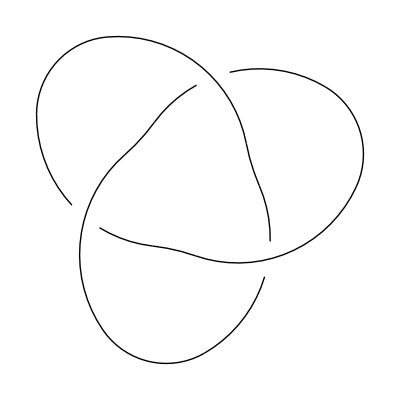

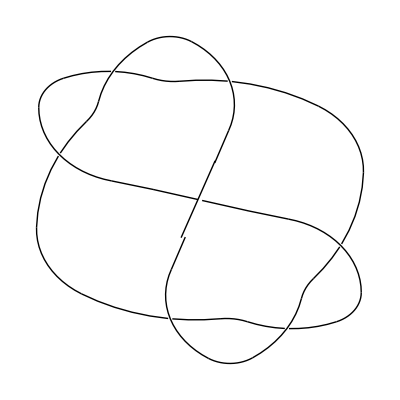

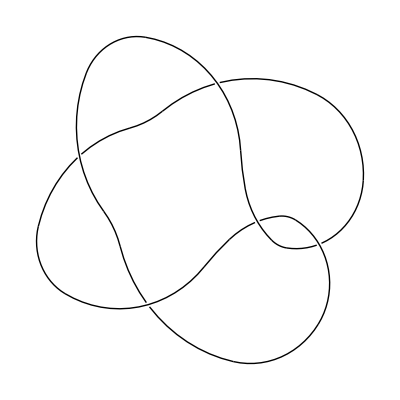

```mathematica
trefoilRight1 = PD[X[1,5,2,4],X[5,3,6,2],X[3,1,4,6]] (*x-z projection*)
trefoilRight2 = PD[X[8,2,9,1],X[2,8,3,7],X[3,12,4,13],X[4,12,5,11],X[10,6,11,5],X[6,14,7,13],X[9,14,10,1]] (*x-y projection*)
trefoilRight3 = PD[X[1,7,2,6],X[2,9,3,10],X[3,9,4,8],X[7,5,8,4],X[5,1,6,10]] (*x-y projection + R1*)
Show[DrawPD[trefoilRight1]]
Show[DrawPD[trefoilRight2]]
Show[DrawPD[trefoilRight3]]
```

```mathematica
LapKh[trefoilRight1]
LapKh[trefoilRight2]
LapKh[trefoilRight3]
s1 = qSpectraAllEigs[trefoilRight1]
s2 = qSpectraAllEigs[trefoilRight2]
s3 = qSpectraAllEigs[trefoilRight3]
```

LapBetti[0,1] = 1

LapBetti[0,3] = 1

LapBetti[0,5] = 0

LapBetti[1,3] = 0

LapBetti[1,5] = 0

LapBetti[2,3] = 0

LapBetti[2,5] = 1

LapBetti[2,7] = 0

LapBetti[3,3] = 0

LapBetti[3,5] = 0

LapBetti[3,7] = 0

LapBetti[3,9] = 1

q+q^3+q^5 t^2+q^9 t^3

q+q^3+q^5 t^2+q^9 t^3

q+q^3+q^5 t^2+q^9 t^3

qSpectraAllEigs[0,1] = {0.}

qSpectraAllEigs[0,3] = {6.,0.}

qSpectraAllEigs[0,5] = {3.}

qSpectraAllEigs[1,3] = {6.,3.,3.}

qSpectraAllEigs[1,5] = {6.,6.,3.}

qSpectraAllEigs[2,3] = {3.,3.,3.}

qSpectraAllEigs[2,5] = {6.,6.,5.,2.,2.,-2.38512×10^-16}

qSpectraAllEigs[2,7] = {4.,1.,1.}

qSpectraAllEigs[3,3] = {3.}

qSpectraAllEigs[3,5] = {5.,2.,2.}

qSpectraAllEigs[3,7] = {4.,1.,1.}

qSpectraAllEigs[3,9] = {0.}

{{{0.},{6.,0.},{3.}},{{6.,3.,3.},{6.,6.,3.}},{{3.,3.,3.},{6.,6.,5.,2.,2.,-2.38512×10^-16},{4.,1.,1.}},{{3.},{5.,2.,2.},{4.,1.,1.},{0.}}}

{{{2.},{8.,5.,4.,3.},{10.9095,8.,7.6093,6.,6.,4.48118},{11.,9.,7.,7.},{9.}},{{2.,2.},{8.,7.36991,7.07302,5.,4.81507,4.63866,4.,4.,3.50457,3.27491,3.,2.83623,2.27801,1.47422,0.735392},{11.4817,10.9828,10.9095,10.6708,10.1028,9.89232,9.71549,8.18018,8.05255,8.,7.6093,7.57429,7.42086,6.76908,6.47458,6.23696,6.13574,6.,6.,5.56166,5.30374,5.276,5.01629,4.80996,4.65685,4.48118,4.48009,4.2036,3.97825,3.36423,3.15843,2.77025,2.33909,2.04108,1.35021},{12.1082,11.9978,11.8157,11.7373,11.1349,11.0478,11.,9.70435,9.14744,9.,8.83407,8.74724,8.71634,8.56893,8.21375,8.11363,7.63613,7.52361,7.02041,7.,7.,6.94437,6.51239,6.35287,6.19298,5.78307,5.50233,5.287,5.03238,4.76454,4.68247,3.52492,3.41806,3.09749,2.83751},{10.2955,10.0853,9.48586,9.48324,9.36418,9.05916,9.,7.83741,7.77235,6.90961,6.7411,5.89145,5.88233,4.73378,4.4587},{7.,7.}},{{2.},{7.36991,7.07302,5.73205,5.,4.81507,4.63866,4.,4.,3.50457,3.27491,3.,2.83623,2.27801,2.26795,1.47422,0.735392},{11.4817,10.9828,10.6708,10.1028,9.89232,9.79847,9.749,9.71549,9.62004,9.51971,9.37277,9.31667,9.07781,9.00815,8.72064,8.18018,8.05255,7.58945,7.57429,7.42086,6.9213,6.76908,6.62022,6.47458,6.46997,6.23696,6.14395,6.13711,6.13574,5.88988,5.70189,5.56166,5.43736,5.33573,5.30374,5.29545,5.276,5.01629,4.97714,4.80996,4.65685,4.48673,4.48009,4.47211,4.28604,4.2036,3.97825,3.8633,3.75359,3.61417,3.53191,3.36423,3.2692,3.16899,3.15843,2.77025,2.50536,2.33909,2.2959,2.04108,1.84386,1.61208,1.59403,1.35021,9.50628×10^-15},{13.4342,13.3652,13.3647,13.27,12.734,12.7336,12.1082,11.9978,11.9662,11.8803,11.8797,11.8157,11.7725,11.7373,11.3759,11.3687,11.2026,11.1349,11.0478,11.0381,10.8068,9.74565,9.70435,9.60367,9.55336,9.52349,9.2792,9.14744,9.07167,8.83407,8.76733,8.7579,8.74724,8.71634,8.56893,8.52691,8.34668,8.2561,8.21375,8.13441,8.11363,7.92951,7.86681,7.69685,7.63613,7.60816,7.52361,7.48026,7.37967,7.30795,7.07562,7.02041,6.94437,6.87078,6.70564,6.5127,6.51239,6.39257,6.35287,6.32772,6.19298,6.05385,5.78307,5.73867,5.70586,5.50233,5.40243,5.35481,5.287,5.27503,5.27059,5.22266,5.03238,4.86233,4.76454,4.73445,4.68247,4.6142,4.5866,4.48559,4.29169,4.24818,4.1436,3.77347,3.70157,3.57875,3.52716,3.52492,3.41806,3.13953,3.09749,3.01381,2.83751,2.81096,2.44067,2.13585,1.91241,1.65113,1.4112,1.77636×10^-15},{12.,12.,11.5906,11.4809,11.4696,11.194,10.9791,10.712,10.6561,10.558,10.4256,10.2955,10.0956,10.0853,9.69952,9.68458,9.64543,9.48586,9.48324,9.37232,9.36418,9.05916,8.52903,8.3219,8.26893,8.10389,8.0727,8.03913,8.03891,7.83741,7.82502,7.77235,7.73819,7.45694,7.20427,7.09883,6.95267,6.90961,6.7411,6.6236,6.60964,6.55765,6.16851,6.14355,6.04328,5.89145,5.88233,5.82724,5.53727,5.15113,4.9402,4.73378,4.72412,4.57708,4.49452,4.4587,4.16335,4.08437,3.9979,3.84503,3.47496,3.40558,2.95706,2.18257,1.2776},{9.,7.91223,7.89195,7.,7.,7.,7.,7.,7.,7.,7.,6.17248,5.28646,5.,3.80131,2.93557},{5.}},{{5.73205,5.,4.,3.,2.26795},{9.79847,9.749,9.62004,9.51971,9.37277,9.31667,9.07781,9.00815,8.72064,8.54973,7.83383,7.58945,7.3588,7.10149,6.9213,6.62022,6.59519,6.46997,6.15602,6.14395,6.13711,6.,5.88988,5.70189,5.43736,5.33573,5.29545,5.29384,5.04798,4.97714,4.48673,4.47211,4.28604,3.90523,3.8633,3.75359,3.61417,3.53191,3.2692,3.16899,2.50536,2.35751,2.2959,1.84386,1.80037,1.61208,1.59403},{13.4342,13.3652,13.3647,13.27,12.734,12.7336,11.9662,11.8803,11.8797,11.8223,11.8014,11.7781,11.7725,11.6897,11.6698,11.6275,11.5564,11.3759,11.3687,11.2841,11.2026,11.0381,10.9586,10.9502,10.826,10.8068,10.7712,10.6162,10.3384,10.3382,10.2622,9.74565,9.60367,9.55336,9.52349,9.47023,9.42082,9.2792,9.07167,8.76733,8.7579,8.69936,8.6229,8.52854,8.52691,8.44396,8.34668,8.2561,8.20186,8.13441,8.01252,7.99673,7.92951,7.90096,7.86681,7.82228,7.69685,7.62675,7.62375,7.60816,7.48026,7.46552,7.37967,7.30795,7.07562,7.06865,6.87078,6.70564,6.5127,6.44384,6.39257,6.32946,6.32772,6.21706,6.19703,6.05385,6.005,5.82355,5.73867,5.70586,5.40243,5.35481,5.27543,5.27503,5.27059,5.22266,5.2056,4.86796,4.86233,4.75641,4.73445,4.68116,4.62521,4.6142,4.5866,4.48559,4.29169,4.24818,4.23672,4.1436,3.96069,3.93196,3.84154,3.77347,3.70492,3.70157,3.57875,3.52716,3.3942,3.36069,3.13953,3.01381,2.81096,2.5521,2.44067,2.20682,2.13585,1.91241,1.89468,1.75338,1.65113,1.4112,0.807688,0.731781},{14.,14.,13.3522,13.3498,12.7704,12.6722,12.6119,12.3753,12.2565,12.1489,12.,12.,12.,12.,11.8491,11.5906,11.5518,11.504,11.4809,11.4696,11.3388,11.3129,11.2422,11.194,11.0678,10.9791,10.8002,10.712,10.6561,10.558,10.4256,10.0956,9.7997,9.78883,9.69952,9.68458,9.64543,9.37232,9.29812,9.26477,9.17881,9.16419,9.0125,8.94595,8.85662,8.71814,8.657,8.52903,8.40233,8.38712,8.3219,8.28208,8.26893,8.25232,8.10389,8.0727,8.04753,8.03913,8.03891,7.99084,7.95235,7.8921,7.82502,7.82332,7.73819,7.51552,7.45694,7.43694,7.20427,7.09883,6.95267,6.9171,6.76303,6.6236,6.60964,6.55765,6.48755,6.22147,6.18339,6.16851,6.14355,6.04328,6.03997,5.82724,5.53727,5.50641,5.30162,5.15113,5.07932,5.04637,4.9402,4.87539,4.72412,4.68601,4.57708,4.55949,4.49452,4.4862,4.39533,4.25386,4.2374,4.16335,4.08926,4.08437,3.9979,3.97123,3.84503,3.79816,3.65966,3.6226,3.51847,3.47496,3.40558,3.25523,3.15609,2.95706,2.79971,2.41458,2.18257,1.80596,1.78956,1.2776,1.14294,1.06563},{10.6169,10.6149,10.1941,10.0929,9.84363,9.57502,9.,8.4482,8.42418,8.22572,8.11113,7.91223,7.89195,7.62195,7.5316,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,6.42859,6.31974,6.17248,6.06707,5.97525,5.42366,5.3715,5.28646,5.28502,5.28342,5.15174,5.,4.17613,3.96526,3.80131,3.62825,3.25958,3.16785,3.15459,3.05304,2.989,2.93557},{5.,5.,5.,5.,5.}},{{8.54973,7.83383,7.3588,7.10149,6.59519,6.15602,6.,5.29384,5.04798,3.90523,2.35751,1.80037},{11.8223,11.8014,11.7781,11.6897,11.6698,11.6275,11.5564,11.2841,10.9586,10.9502,10.826,10.7712,10.6162,10.3384,10.3382,10.2622,10.,10.,10.,10.,9.77029,9.47023,9.42082,8.71239,8.69936,8.62589,8.6229,8.56155,8.52854,8.44396,8.20186,8.01252,7.99673,7.90096,7.82228,7.70692,7.62675,7.62375,7.46552,7.36078,7.06865,6.44384,6.32946,6.21706,6.19703,6.005,5.82355,5.27543,5.2056,5.02886,4.96613,4.86796,4.75641,4.68116,4.62521,4.43845,4.27691,4.23672,3.96069,3.93196,3.84154,3.70492,3.3942,3.36069,2.5521,2.20682,1.89468,1.75338,1.55183,0.807688,0.731781},{14.,14.,13.9038,13.7101,13.7097,13.5565,13.3522,13.3498,12.9532,12.8473,12.7704,12.6722,12.6119,12.3753,12.2565,12.1878,12.1805,12.1489,12.1113,12.0289,12.,12.,11.9479,11.8491,11.6223,11.5518,11.504,11.4073,11.3474,11.3388,11.3129,11.2434,11.2422,11.0678,10.8002,10.,9.86397,9.7997,9.78883,9.73192,9.29812,9.28363,9.26535,9.26477,9.17881,9.16419,9.0125,8.94595,8.85662,8.71814,8.657,8.48091,8.40233,8.38712,8.34158,8.28208,8.25485,8.25232,8.04753,7.99084,7.95235,7.8921,7.82332,7.76687,7.51552,7.48867,7.43694,6.9171,6.88367,6.86206,6.76303,6.57273,6.48755,6.3513,6.22147,6.19043,6.18339,6.03997,5.99477,5.50641,5.30162,5.07932,5.06294,5.04637,4.87539,4.85359,4.68601,4.58519,4.55949,4.4862,4.39533,4.25386,4.2374,4.19521,4.17552,4.08926,3.97123,3.93422,3.79816,3.65966,3.65869,3.6226,3.51847,3.25523,3.15609,3.10498,2.89627,2.85323,2.79971,2.41458,1.8977,1.80596,1.78956,1.14294,1.06563,0.992161,0.700225,-2.75691×10^-15},{11.461,11.3808,11.3757,11.2737,10.9037,10.7704,10.7221,10.6169,10.6149,10.5648,10.4407,10.1941,10.1852,10.0929,9.84363,9.76785,9.57502,9.1982,8.97379,8.91253,8.58561,8.4482,8.42418,8.22572,8.11113,7.62195,7.5316,7.0519,7.00472,7.,7.,7.,7.,6.66854,6.45103,6.42859,6.31974,6.31265,6.06707,5.97525,5.82974,5.80567,5.7712,5.42366,5.3715,5.29884,5.28502,5.28342,5.15174,5.02132,4.77018,4.2083,4.17613,4.17127,3.96526,3.81824,3.68347,3.62825,3.25958,3.22781,3.21387,3.16785,3.15459,3.05304,3.01688,2.989,1.98608,1.98302,1.21579,0.521377,0.452078},{6.,6.,5.,5.,5.,5.,5.,5.,5.,5.,2.,2.}},{{10.,10.,10.,10.,9.77029,8.71239,8.62589,8.56155,7.70692,7.36078,5.02886,4.96613,4.43845,4.27691,1.55183},{13.9038,13.7101,13.7097,13.5565,12.9532,12.8473,12.1878,12.1805,12.1113,12.0289,12.,12.,12.,11.9479,11.6223,11.4073,11.3474,11.3078,11.2434,10.5244,10.,10.,9.86397,9.73192,9.28363,9.26535,8.48091,8.34158,8.25485,7.76687,7.48867,6.88367,6.86206,6.57273,6.3513,6.19043,5.99477,5.06294,4.85359,4.58519,4.19521,4.17552,4.16779,3.93422,3.65869,3.10498,2.89627,2.85323,1.8977,0.992161,0.700225},{12.9186,12.8284,12.4567,12.3263,11.8144,11.6766,11.461,11.3808,11.3757,11.2737,10.9037,10.7704,10.7221,10.5648,10.4407,10.1852,9.76785,9.1982,8.97379,8.91253,8.58561,7.75535,7.17157,7.0519,7.00472,6.79669,6.66854,6.66318,6.45103,6.31265,5.82974,5.80567,5.7712,5.29884,5.02132,4.77018,4.52647,4.50525,4.2083,4.17127,3.81824,3.68347,3.22781,3.21387,3.01688,2.5605,1.98608,1.98302,1.21579,0.521377,0.452078},{6.73205,6.,6.,6.,6.,5.41421,5.,5.,5.,5.,3.26795,2.58579,2.,2.,-1.18859×10^-16}},{{12.,12.,12.,11.3078,10.5244,10.,4.16779},{14.,12.9186,12.8284,12.4567,12.3263,11.8144,11.6766,7.75535,7.17157,6.79669,6.66318,4.52647,4.50525,2.5605},{7.,6.73205,6.,6.,5.41421,3.26795,2.58579}},{{14.},{7.}}}

{{{1.},{7.04892,2.6431,2.30798},{8.38849,5.18728,3.42423},{6.}},{{1.},{7.04892,5.81361,3.52932,3.,2.6431,2.30798,1.65708,-7.15698×10^-17},{9.65188,9.61889,9.,8.38849,8.22739,5.84427,5.18728,4.29024,4.,3.42423,3.05706,2.61973,1.69053,-4.25864×10^-15},{8.,7.65109,6.44949,6.,6.,4.72611,3.6228,1.55051},{4.}},{{5.81361,3.52932,3.,3.,1.65708},{9.65188,9.61889,9.,8.22739,8.,7.71959,7.58423,6.59798,5.84427,5.70572,5.57096,4.29024,4.18542,4.,3.10635,3.05706,2.61973,1.71005,1.69053,0.819705},{10.,10.,9.39239,8.82216,8.33018,8.23659,8.,7.65109,6.44949,6.,6.,5.09662,4.82821,4.72611,4.30376,3.6228,3.09397,1.71568,1.55051,1.18043},{6.73205,4.,4.,4.,3.26795}},{{3.},{8.,7.71959,7.58423,6.59798,6.,5.70572,5.57096,5.41421,4.18542,3.10635,2.58579,1.71005,0.819705},{10.,10.,10.,9.39239,9.28856,8.82216,8.62481,8.33018,8.28317,8.23659,6.,5.8511,5.09662,5.03603,4.82821,4.30376,3.21217,3.09397,2.83924,2.,1.71568,1.18043,0.864921,3.1379×10^-15},{7.71838,7.33685,6.73205,6.64374,5.23607,4.,4.,3.79329,3.26795,2.,1.93378,0.763932,0.573963},{2.}},{{6.,5.41421,2.58579},{10.,9.28856,8.62481,8.28317,8.,5.8511,5.03603,3.21217,2.83924,2.,0.864921},{9.,7.71838,7.33685,6.64374,5.23607,4.,3.79329,2.,1.93378,0.763932,0.573963},{3.,2.,-3.92481×10^-17}},{{8.},{9.,4.},{3.}}}

## \Delta^{0,3} and \Delta^{1,5}

```mathematica
CC[trefoilRight1,-1,3]
CC[trefoilRight1,0,3]
CC[trefoilRight1,1,3]
```

{0}

{v[0,0,0] vm[2] vp[1],v[0,0,0] vm[1] vp[2]}

{v[0,0,1] vm[1],v[0,1,0] vm[1],v[1,0,0] vm[1]}

```mathematica
d[trefoilRight1][#] &/@ CC[trefoilRight1,-1,3]
d[trefoilRight1][#] &/@ CC[trefoilRight1,0,3]
```

{0}

{v[0,0,1] vm[1]+v[0,1,0] vm[1]+v[1,0,0] vm[1],v[0,0,1] vm[1]+v[0,1,0] vm[1]+v[1,0,0] vm[1]}

```mathematica
GetDQ[trefoilRight1, 0, 3]// MatrixForm (*check above agrees with package *)
GetDQ[trefoilRight1, 1, 3] // MatrixForm (*check above agrees with package *)
Transpose[GetDQ[trefoilRight1, 1, 3]].GetDQ[trefoilRight1, 1, 3] // MatrixForm (*manual computation*)
qLapNew[trefoilRight1,0,3] // MatrixForm (*fact check*)
Eigenvalues[qLapNew[trefoilRight1,0,3]]
```

(0
0)

(1 | 1
1 | 1
1 | 1)

(3 | 3
3 | 3)

(3 | 3
3 | 3)

{6,0}

```mathematica
CC[trefoilRight1,0,5]
CC[trefoilRight1,1,5]
CC[trefoilRight1,2,5]
```

{v[0,0,0] vp[1] vp[2]}

{v[0,0,1] vp[1],v[0,1,0] vp[1],v[1,0,0] vp[1]}

{v[0,1,1] vm[3] vp[1],v[0,1,1] vm[1] vp[3],v[1,0,1] vm[2] vp[1],v[1,0,1] vm[1] vp[2],v[1,1,0] vm[2] vp[1],v[1,1,0] vm[1] vp[2]}

```mathematica
d[trefoilRight1][#] &/@ CC[trefoilRight1,0,5]
```

{v[0,0,1] vp[1]+v[0,1,0] vp[1]+v[1,0,0] vp[1]}

```mathematica
d[trefoilRight1][#] &/@ CC[trefoilRight1,1,5]
```

{v[1,0,1] vm[2] vp[1]+v[0,1,1] vm[3] vp[1]+v[1,0,1] vm[1] vp[2]+v[0,1,1] vm[1] vp[3],v[1,1,0] vm[2] vp[1]-v[0,1,1] vm[3] vp[1]+v[1,1,0] vm[1] vp[2]-v[0,1,1] vm[1] vp[3],-v[1,0,1] vm[2] vp[1]-v[1,1,0] vm[2] vp[1]-v[1,0,1] vm[1] vp[2]-v[1,1,0] vm[1] vp[2]}

```mathematica
qLapNew[trefoilRight1,1,5] // MatrixForm
Eigenvalues[qLapNew[trefoilRight1,1,5]]
```

(5 | -1 | -1
-1 | 5 | -1
-1 | -1 | 5)

{6,6,3}

```mathematica
Transpose[GetDQ[trefoilRight1, 2, 5]].GetDQ[trefoilRight1, 2, 5] //MatrixForm
```

(4 | -2 | -2
-2 | 4 | -2
-2 | -2 | 4)